Autor: Adam Paździerz

# Metody numeryczne

## (kierunek Informatyka)

## Projekt 6

Aproksymacja średniokwadratowa dyskretna

Napisać procedurę realizującą algorytm aproksymacji średniokwadratowej dyskretnej. 
Działanie procedury przetestować na przykładzie z wykładu.

a) Aproksymować punkty (x_i, cos x_i) dla x_i=-6,-5,...,5,6, wielomianem stopnia czwartego. Jako funkcję wagową raz przyjąć funkcję w(x)=1, natomiast drugi raz funkcję w(x)={10 | dla |x|≤2,
10^-10 | dla |x|>2.
Wykreślić na wspólnym rysunku otrzymane wielomiany oraz punkty aproksymacji.

b) Zmianę temperatury płynu w zbiorniku ilustruje następująca tabela:

t[s] | 0 | 60 | 120 | 180 | 240 | 300
T[°C] | 100 | 90 | 80 | 72 | 65 | 58

Aproksymować temperaturę funkcją postaci T(t)=a exp(b  t). Jako funkcję wagową przyjąć w(t)=1. Policzyć temperaturę płynu po 200 s od chwili początkowej.

## Rozwiązanie

### Program

```mathematica
ClearAll[φ];
```

```mathematica
φ[0][x_]:=1;
φ[i_][x_]:=x^i;
(*φ - funkcja bazowa *)
```

```mathematica
aproksymacja [φ_,xx_,yy_,w_]:=Module [{f,m,l,d,i,j,k,a,F},
m=Length[φ];
l=Length[xx];
f=φ;
For[k=1,k≤m,k++,
f[[k]]=Sum[w[xx[[j]]]*yy[[j]]*(φ[[k]]/.{x->xx[[j]]}),{j,1,l}];
];

d=Table[0,{m},{m}];
For[k=1,k≤m,k++,
For[i=1,i≤k,i++,
d[[i,k]]=Sum[w[xx[[j]]]*(φ[[i]]/.{x->xx[[j]]})*(φ[[k]]/.{x->xx[[j]]}),{j,1,l}];
If[i≠k,
d[[k,i]]=d[[i,k]];
];

];
];

a=LinearSolve[d,f];
F=Sum[a[[j]]*φ[[j]],{j,1,m}];

Return[F];
]
```

### Przykład testowy

```mathematica
x1={0,1,2,3};
y1={1,-1,2,4};
w[x_]:=1;
aproksymacja[{φ[0][x],φ[1][x],φ[2][x]},x1,y1,w]
```

7/10-(9 x)/5+x^2

### Zadanie a)

```mathematica
Clear[xa,ya,wa];
xa=Table[i,{i,-6,6}];
ya=Table[N[Cos[i]],{i,-6,6}];
wa[x_]:=1;

zada1=aproksymacja[{φ[0][x],φ[1][x],φ[2][x],φ[3][x],φ[4][x]},xa,ya,wa]
```

0.43536-0.141988 x^2+0.00453425 x^4

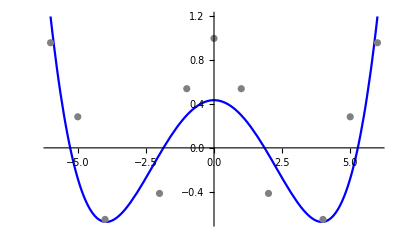

```mathematica
r1=Show[Plot[zada1,{x,-6,6},PlotStyle->Blue],ListPlot[Thread[{xa,ya}],PlotStyle->{Gray}]]
```

```mathematica
Clear[wa2];
wa2[x_]:=10/;Abs[x]≤2;
wa2[x_]:=10^-10;
```

```mathematica
zada2=aproksymacja[{φ[0][x],φ[1][x],φ[2][x],φ[3][x],φ[4][x]},xa,ya,wa2]
```

1.+7.37622×10^-17 x-0.494918 x^2-2.08034×10^-17 x^3+0.0352202 x^4

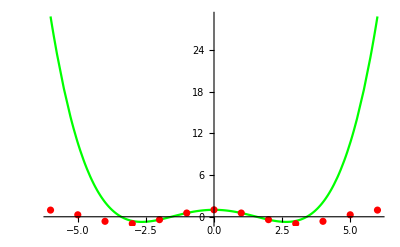

```mathematica
r2=Show[Plot[zada2,{x,-6,6},PlotStyle->Green],ListPlot[Thread[{xa,ya}],PlotStyle->{Red}]]
```

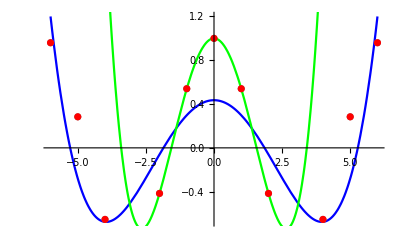

```mathematica
Show[r1,r2]
```

### Zadanie b)

```mathematica
Clear[t,T,wb];
(*T(t)=a exp (b t)/ln()
ln T(t)=ln(a exp(b t))
ln T(t)=ln a+b t
y=c+bx
gdzie y=lnT[t],c=lna*)
```

```mathematica
t={0,60,120,180,240,300};
T={100,90,80,72,65,58};
wb[x_]:=1;
dane=Transpose[{t,T}]
```

{{0,100},{60,90},{120,80},{180,72},{240,65},{300,58}}

```mathematica
logT=Log[T]
```

{Log[100],Log[90],Log[80],Log[72],Log[65],Log[58]}

```mathematica
Zad2=aproksymacja[{φ[0][x],φ[1][x]},t,logT,wb]
```

(x (5 Log[58]+3 Log[65]+Log[72]-Log[80]-3 Log[90]-5 Log[100]))/2100+1/21 (-4 Log[58]-Log[65]+2 Log[72]+5 Log[80]+8 Log[90]+11 Log[100])

```mathematica
c=Zad2⟦2⟧;
b=Zad2[[1]]/.{x->1};
a=Exp[c];
```

```mathematica
tem[t_]:=a* Exp[b*t]
```

```mathematica
(*Temperatura po 200s*)
```

```mathematica
tem[200.]
```

69.5804